## Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Маркаров М.Г. Группа: ТФ-13-22 Задача № 1 -Graphics-

#### Данные из условия: d2=130(mm);δ=4(mm) - геометрия труб ; tAir=10 (°C)-температура воздуха;tLiquid1=110(°C)-температура горячей воды на входе (как t_ж1) ; p=5(MPa)- давление горячей воды;w=21(km/h) - скорость течения горячей воды; λMinWool=0.045(W/m*K);δMinWool=50(mm); tLiquid2=110-30=80(°C)-температура горячей воды на выходе(как t_ж2) ; λConcrete=1.1(W/m K);δConcrete=50(mm);ϵ=0.8-излучательная способность поверхности материала труб; α= 9.6(W/m^2K)-коэффициент теплоотдачи

```mathematica
d2=130*10^-3;δ=4*10^-3;tAir=10;tLiquid1=110;p=5*10^6;w=21/3.6;λMinWool=0.045;δMinWool=50*10^-3;tLiquid2=80;λConcrete=1.1;δConcrete=50*10^-3;
ϵ=0.8;
α=9.6;
```

#### Сталь берем нержавеющую, ее коэффициент теплопроводности λSteel (W/m K) берем как const в виду слабой зависимости от температуры:

```mathematica
λSteel=14.4 ;
```

#### Изобарную (p=5MPa)теплоемкость и плотность воды при tLiquid1 и tLiquid2 найдем через REFPROP: cp: tLiquid1=110 (°C) cp1=4.2169 (kJ/kg K) -Graphics-

#### tLiquid2=80 (°C) cp2=4.1863 (kJ/kg K) -Graphics- плотность: tLiquid1=110 (°C) ρ1=953.25 (kg/m^3) -Graphics- tLiquid2=80 (°C) ρ2=973.94 (kg/m^3) -Graphics-

```mathematica
cp1=4.2169;cp2=4.1863 ;ρ1=953.25;ρ2=973.94 ;
```

#### Средняя удельная изобарная теплоемкость cpAverage(kJ/kg K)

```mathematica
cpAverage=(cp1+cp2)/2
```

4.2016

#### Средняя плотность воды ρAverage (kg/m^3)

```mathematica
ρAverage=(ρ1+ρ2)/2
```

963.595

#### Массовый расход воды G(kg/s)

```mathematica
G=π*((d2-2*δ)/2)^2*w*ρAverage
```

65.7084

#### Найдем диаметры d1, d3 (m)

```mathematica
d1=d2-2δ//N
```

0.122

```mathematica
d3=d2+2δ//N
```

0.138

#### Найдем линейный коэффициент теплопередачи для трубы с ватной изоляцией KlinearMinWool (W/m K)

```mathematica
KlinearMinWool=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/(α*d3))
```

0.439675

#### Применяя формулу Шухова найдем расстояние(длину трубы) на котором будет выполняться условие разности температур на входе и выходе в трубу с изоляцией из минеральной ваты:

```mathematica
First[NSolve[tLiquid2==tAir+(tLiquid1-tAir)*Exp[-KlinearMinWool/(G*cpAverage)*π*x],x]]
```

{x→71.2897}

#### Таким образом длина трубы равна 71.289696m)

```mathematica
L=71.289696;
```

#### Найдем линейный коэффициент теплопередачи для трубы с бетонной изоляцией KlinearConcrete (W/m K)

```mathematica
KlinearConcrete=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/(α*d3))
```

0.610498

#### По формуле Шухова найдем температуру на выходе из трубы с бетонной изоляцией:

```mathematica
t[x_,k_]:=tAir+(tLiquid1-tAir)*Exp[-k/(G*cpAverage)*π*x]
```

```mathematica
t[L,KlinearConcrete]
```

70.9418

#### Найдем линейный коэффициент теплопередачи для трубы без изоляции KlinearRaw (W/m K)

```mathematica
KlinearRaw=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(α*d3))
```

0.620786

#### По формуле Шухова найдем температуру на выходе из трубы без изоляции:

```mathematica
t[L,KlinearRaw]
```

70.4353

#### Функция теплового потока и плотности теплового потока :

```mathematica
Q[x_,k_]:=k*π*(t[x,k]-tAir)*x;
qLinear[x_,k_]:=k*π*(t[x,k]-tAir);
```

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для голой трубы:

```mathematica
Q[L,KlinearRaw]
```

8402.51

```mathematica
qLinear[L,KlinearRaw]
```

117.864

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с бетонной изоляцией:

```mathematica
Q[L,KlinearConcrete]
```

8332.52

```mathematica
qLinear[L,KlinearConcrete]
```

116.882

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с ватной изоляцией:

```mathematica
Q[L,KlinearMinWool]
```

6892.97

```mathematica
qLinear[L,KlinearMinWool]
```

96.6895

### Произведем расчеты по другому:

```mathematica
qLinearAdditional[k_]:=k*π*((tLiquid1+tLiquid2)/2-tAir)
```

#### Запишем баланс энергий: Q=qLinear*L=G*cpAverage*(tLiquid1-tLiquid2)=π *(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2),отсюда можно найти L:

```mathematica
NSolve[qLinearAdditional[KlinearMinWool]*x==π*(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2),x]
```

{{x→70.5434}}

#### Таким образом длина трубы по этому способу равна Ladditional(m)

```mathematica
Ladditional=70.543417;
```

#### Выразим tLiquid2 из линейной плотности теплового потока как переменную :

```mathematica
Solve[k*π*((tLiquid2asVariable+tLiquid1)/2-tAir)*x==π*(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2asVariable),tLiquid2asVariable]
```

{{tLiquid2asVariable→(30368.8-141.372 k x)/(276.08+1.5708 k x)}}

```mathematica
tLiquid2asVariable[k_,x_]:=(30368.844-141.37167*k*x)/(276.0804+1.5707963 *k*x)
```

#### Теперь найдем температуры на выходе из трубы с бетонной изоляцией и трубы без изоляции. Бетонная изоляция:

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

70.6383

#### Голая труба:

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

70.1073

#### Изобразим функциональные зависимости температуры жидкости в точке χ, где χ-обобщенное расстояние(длина трубы)

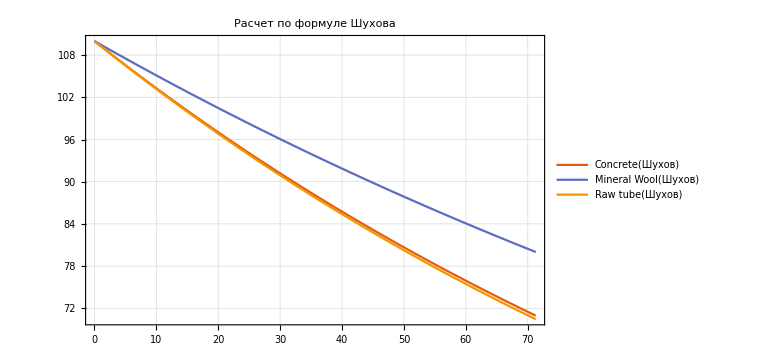

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw]},{χ,0,L},PlotLabel->"Расчет по формуле Шухова",PlotTheme->"Scientific",PlotLegends->{"Concrete(Шухов)","Mineral Wool(Шухов)","Raw tube(Шухов)"},ImageSize->Large,GridLines->Automatic]
```

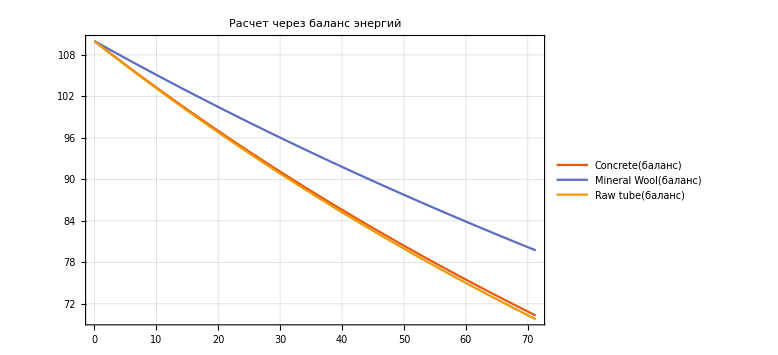

```mathematica
Plot[{tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Расчет через баланс энергий",PlotTheme->"Scientific",PlotLegends->{"Concrete(баланс)","Mineral Wool(баланс)","Raw tube(баланс)"},ImageSize->Large,GridLines->Automatic]
```

#### Сопоставим функции температур в одной системе координат:

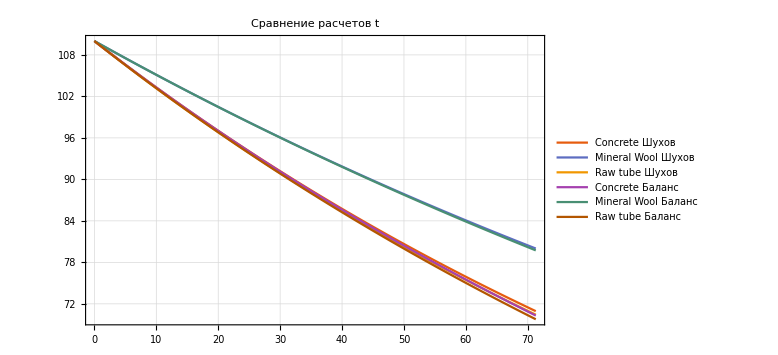

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Точно так же изобразим функции линейных плотностей тепловых потоков. Для начала введем функцию линейной плотности теплового потока при расчете методом баланса энергий:

```mathematica
qLinearAdditionalFunction[k_]:=k*π*((tLiquid1-tLiquid2)/2-tAir)
```

#### Покажем графики линейных плотностей тепловых потоков в одной координатной плоскости ql(W/m):

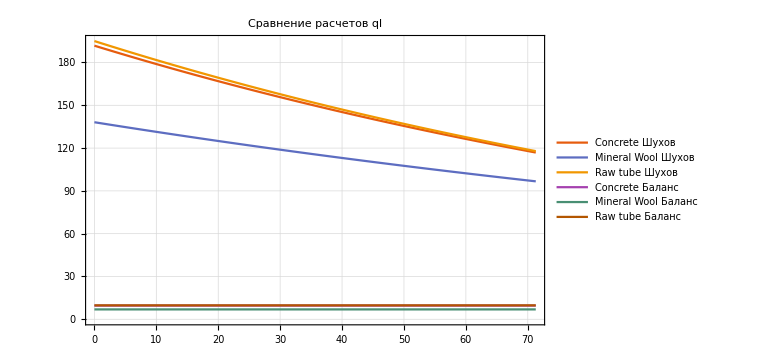

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearAdditionalFunction[KlinearConcrete],qLinearAdditionalFunction[KlinearMinWool],qLinearAdditionalFunction[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов ql",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Теперь построим поверхностные плотности тепловых потоков qc (W/m^2):

```mathematica
qcShuhov[x_,k_]:=qLinear[x,k]/(π*d1);qcBalance[k_]:=qLinearAdditionalFunction[k]/(π*d1);
```

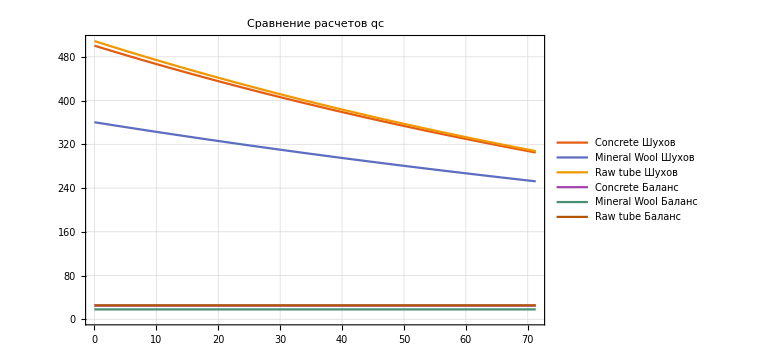

```mathematica
Plot[{qcShuhov[χ,KlinearConcrete],qcShuhov[χ,KlinearMinWool],qcShuhov[χ,KlinearRaw],qcBalance[KlinearConcrete],qcBalance[KlinearMinWool],qcBalance[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов qc",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Найдем среднее значение линейной плотности теплового потока(W/m):

```mathematica
qLinearAverageWithoutInsulation=(qLinear[0,KlinearRaw]+qLinear[L,KlinearRaw])/2
```

156.445

```mathematica
qLinearAverageConcreteInsulation=(qLinear[0,KlinearConcrete]+qLinear[L,KlinearConcrete])/2
```

154.338

```mathematica
qLinearAverageMinWoolInsulation=(qLinear[0,KlinearMinWool]+qLinear[L,KlinearMinWool])/2
```

117.409

#### Среднее значение температуры на поверхности труб:

```mathematica
NSolve[{qLinearAverageWithoutInsulation==π*(twWithoutIns-tAir)/(1/(α*d2)),qLinearAverageConcreteInsulation==π*(twConcreteIns-tAir)/(1/(α*d3)),qLinearAverageMinWoolInsulation==π*(twMinWoolIns-tAir)/(1/(α*d3))},{twWithoutIns,twConcreteIns,twMinWoolIns}]
```

NSolve::ivar: 49.9022 is not a valid variable.

NSolve[{False,False,False},{49.9022,47.0828,38.2098}]

```mathematica
twWithoutIns=49.902233;twConcreteIns=47.0828314;twMinWoolIns=38.209809;
```

#### Учтем излучение σ- константа Стефана-Больцмана(W/m^2 K^4)

```mathematica
σ=5.671*10^-8;
```

#### Переведем температуры на поверхности труб и температуру воздуха в абсолютные единицы(Кельвины)

```mathematica
TwWithoutIns=twWithoutIns+273.15;TwConcreteIns=twConcreteIns+273.15;TwMinWoolIns=twMinWoolIns+273.15;Tair=tAir+273.15;
```

#### Найдем результирующую плотность потока излучения Eres(W/m^2):

```mathematica
EresMinWool=ϵ*σ*(TwMinWoolIns^4-Tair^4)
```

134.764

```mathematica
EresConcrete=ϵ*σ*(TwConcreteIns^4-Tair^4)
```

185.485

```mathematica
EresWithoutIns=ϵ*σ*(TwWithoutIns^4-Tair^4)
```

202.51

#### Найдем эквивалентный коэффициент теплоотдачи излучением αEqv (W/m^2K):

```mathematica
αEqvMinWool=EresMinWool/(TwMinWoolIns-Tair)
```

4.7772

```mathematica
αEqvConcrete=EresConcrete/(TwConcreteIns-Tair)
```

5.00191

```mathematica
αEqvWithoutIns=EresWithoutIns/(TwWithoutIns-Tair)
```

5.07516

```mathematica
MradMinWool=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/((α+αEqvMinWool)*d3)
```

2.0236

```mathematica
MradConcrete=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3)
```

1.37944

```mathematica
MradWithoutIns=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3)
```

1.34982

```mathematica
P=(d1/2)^2*w*ρAverage*cpAverage
```

87.8791

```mathematica
tLiquid2RadiationVariable[M_,x_]:=(2*P*M*tLiquid1+2*tAir*x - tLiquid1*x)/(x+2*P*M)
```

#### Линейная плотность потока излучения для трубы с ватной изоляцией:

```mathematica
qLinearRadiationMinWool[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradMinWool,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))
```

#### Из баланса энергий найдем длину трубы:

```mathematica
NSolve[((tLiquid1+tLiquid2)/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))*Len ==π*(d1/2)^2*w*ρAverage*cpAverage*(tLiquid1-tLiquid2),Len]
```

{{Len→135.168}}

#### Если учитывать излучение тогда длина трубы будет другой(m):

```mathematica
LwithRadiation=135.1683998;
```

#### Линейная плотность потока излучения трубы с ватной изоляцией:(W/m)

```mathematica
qLinearRadiationMinWool[LwithRadiation]
```

164.104

#### Для трубы без изоляции:(W/m^2)

```mathematica
qLinearRadiationWithoutIns[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradWithoutIns,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3))
```

```mathematica
qLinearRadiationWithoutIns[LwithRadiation]
```

148.267

```mathematica
tLiquid2RadiationVariableWithoutIns=tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

37.4087

#### Для трубы с изоляцией из бетона:

```mathematica
qLinearRadiationConcrete[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradConcrete,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3))
```

```mathematica
qLinearRadiationConcrete[LwithRadiation]
```

146.223

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

38.4096

#### Рассчитаем потери теплоты:

```mathematica
QradConcrete[x_]:=qLinearRadiationConcrete[x]*x;
QradMinWool[x_]:=qLinearRadiationMinWool[x]*x;
QradWithoutIns[x_]:=qLinearRadiationWithoutIns[x]*x;
```

#### Потери теплоты в трубе с бетонной изоляцией:(W)

```mathematica
QradConcrete[LwithRadiation]
```

19764.7

#### Потери теплоты в трубе с ватной изоляцией:(W)

```mathematica
QradMinWool[LwithRadiation]
```

22181.7

```mathematica
QradWithoutIns[LwithRadiation]
```

20041.

#### Сравним расчеты температуры(Шухов/Излучение):

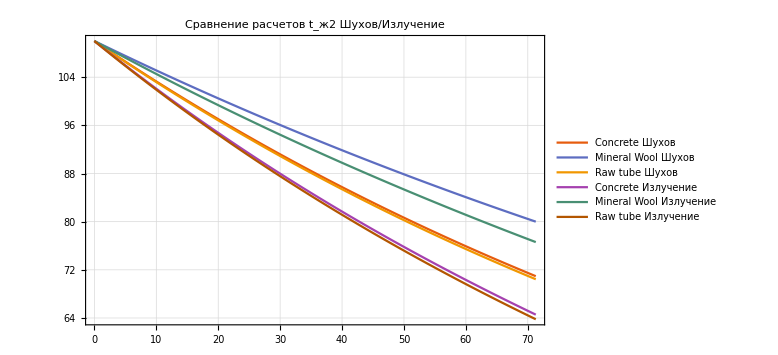

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2RadiationVariable[MradConcrete,χ],tLiquid2RadiationVariable[MradMinWool,χ],tLiquid2RadiationVariable[MradWithoutIns,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t_(:04362) Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Сравним расчеты линейной плотности потоков тепла/излучения(Шухов/Излучение):

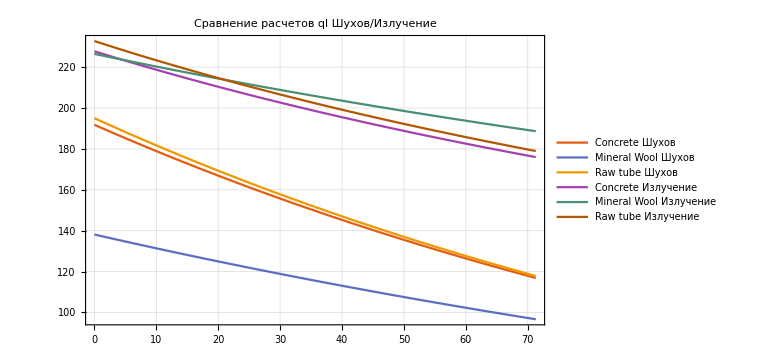

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearRadiationConcrete[χ],qLinearRadiationMinWool[χ],qLinearRadiationWithoutIns[χ]},{χ,0,L},PlotLabel->"Сравнение расчетов ql Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Соберем все результаты выше воедино. Способ основанный на формуле Шухова. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
t[L,KlinearConcrete]
```

70.9418

```mathematica
t[L,KlinearMinWool]
```

80.

```mathematica
t[L,KlinearRaw]
```

70.4353

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Q[L,KlinearConcrete]
```

8332.52

```mathematica
Q[L,KlinearMinWool]
```

6892.97

```mathematica
Q[L,KlinearRaw]
```

8402.51

#### Способ основанный на методе баланса энергии. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

70.6383

```mathematica
tLiquid2asVariable[KlinearMinWool,Ladditional]
```

80.

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

70.1073

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Qadditional[k_,x_]:=qLinear[x,k]*x;
```

```mathematica
Qadditional[KlinearConcrete,Ladditional]
```

8288.15

```mathematica
Qadditional[KlinearMinWool,Ladditional]
```

6846.32

```mathematica
Qadditional[KlinearRaw,Ladditional]
```

8358.5

#### Способ с учетом излучения.Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

38.4096

```mathematica
tLiquid2RadiationVariable[MradMinWool,LwithRadiation]
```

54.9228

```mathematica
tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

37.4087

#### Поток излучения(W):(порядок:бетон,вата,без изоляции)

```mathematica
QradConcrete[LwithRadiation]
```

19764.7

```mathematica
QradMinWool[LwithRadiation]
```

22181.7

```mathematica
QradWithoutIns[LwithRadiation]
```

20041.

#### Найдем критический диаметр при бетонной и ватной изоляциях

```mathematica
d2//N
```

0.13

```mathematica
dCriticalConcrete=d2+(2λConcrete)/α
```

0.359167

#### Мы не дотягиваем до критического диаметра и поэтому изоляция из бетона не эффективна.

```mathematica
dCriticalMinWool=d2+(2λMinWool)/α
```

0.139375

#### Мы близки к критическому диаметру, но изоляция все равно не эффективна, ее нужно увеличить до критического, а потом и до эффективного диаметра для существенного уменьшения потерь.